```mathematica
normalConst = Integrate[(x+lbk)^zs*Exp[-x],{x,0,Infinity}]
```

38

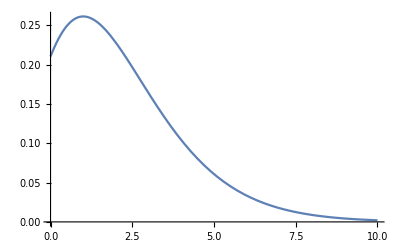

```mathematica
Plot[(x+lbk)^zs*Exp[-x]/normalConst,{x,0,10}]
```

```mathematica
FindMaximum[Exp[-x]*(x+zbk)^zs,x]
```

{307285.,{x→4.}}

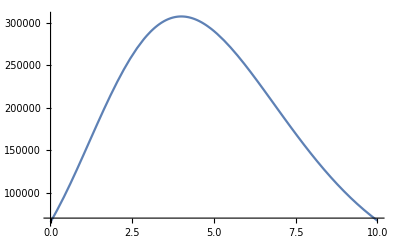

```mathematica
Plot[Exp[-x]*(x+zbk)^zs,{x,0,10}]
```

```mathematica
Integrate[(x+lbk)^zs*Exp[-x]/normalConst,{x,0,Infinity}]
```

1

```mathematica
probDist=ProbabilityDistribution[(x+lbk)^zs*Exp[-x]/normalConst,{x,0,Infinity}];
```

```mathematica
mu=N[Mean[probDist]]
sig=N[StandardDeviation[probDist]]
```

2.42105

1.84436

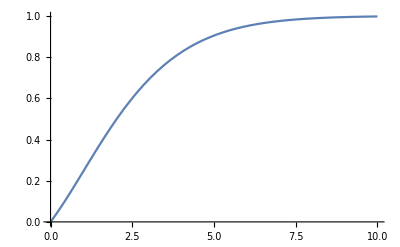

```mathematica
Plot[CDF[probDist,x],{x,0,10}]
```

```mathematica
Plot[PDF[probDist,x],{x,0,10}]
```

-Graphics-

we want it to be larger than 99,7%

```mathematica
1-N[Probability[x>mu+3.3*sig,x\[Distributed]probDist]]
```

0.991707

```mathematica
NSolve[N[CDF[probDist,a]]==0.99,a]
```

NSolve[(Piecewise[{{5.01743550102×10^-5201 (1.9930500348×10^5200-1. Gamma[1838.,1803.+a]), a>0.}, {0., True}}])==0.99,a]

```mathematica
mu+3.3*sig
```

158.698

```mathematica
NSolve[N[Probability[x>a,x\[Distributed]probDist]]==0.01,a]
```

NSolve[(Piecewise[{{1., a≤0.}, {-1.20504×10^-12+5.01743550102×10^-5201 Gamma[1838.,1803.+a], True}}])==0.01,a]

```mathematica
lbkDist = PDF[GammaDistribution[zbk+1,1],x];
```

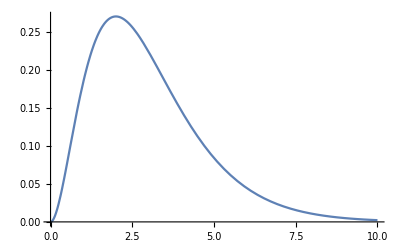

```mathematica
Plot[lbkDist,{x,0,10}]
```

i think transformed distribution is for transforming the actual random variable (lsg in this case) and NOT for making a probability distribution where a parameter of the distribution (lbk) has itself a distribution

```mathematica
lsgTest=1
finalDist=TransformedDistribution[(lsgTest+lbk2)^zs*Exp[-lsgTest],lbk2\[Distributed]GammaDistribution[zbk+1,1]]
```

1

TransformedDistribution[(1+lbk2)^3/ⅇ,lbk2\[Distributed]GammaDistribution[3,1]]

```mathematica
PDF[finalDist,lbk2]
```

Piecewise[{{(ⅇ^(1-Root[1-ⅇ lbk2+3 #1+3 #1^2+#1^3&,1]) Root[1-ⅇ lbk2+3 #1+3 #1^2+#1^3&,1]^2)/(6 (1+Root[1-ⅇ lbk2+3 #1+3 #1^2+#1^3&,1])^2), lbk2>1/ⅇ&&Root[1-ⅇ lbk2+3 #1+3 #1^2+#1^3&,1]>0}, {0, True}}]

```mathematica
NIntegrate[PDF[finalDist,lsg],{lsg,0,Infinity}]
```

1.

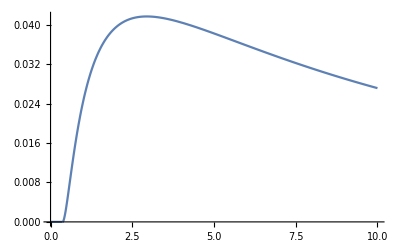

```mathematica
Plot[PDF[finalDist,x],{x,0,10}]
```

End of the tries with transformed distribution

```mathematica
probDist2=ProbabilityDistribution[(lsg+lbk)^zs*Exp[-lsg]/(Exp[lbk]* Gamma[1+zs,lbk]),{lsg,0,Infinity}]
```

ProbabilityDistribution[((2+x)^5 ⅇ^(-2-x))/Gamma[6,2],{x,0,∞}]

```mathematica
Assuming[lbk>0,Integrate[(lsg+lbk)^zs*Exp[-lsg],{lsg,0,Infinity}]]
```

ⅇ^lbk Gamma[1+zs,lbk]

```mathematica
Assuming[lbk>0,Mean[probDist2]]
```

(ⅇ^-lbk (lbk^(2+zs)+ⅇ^lbk Gamma[2+zs,lbk]-ⅇ^lbk lbk Gamma[2+zs,lbk]+ⅇ^lbk zs Gamma[2+zs,lbk]))/((1+zs) Gamma[1+zs,lbk])

```mathematica
D[PDF[probDist2,x],x]
```

Piecewise[{{0, x<0}, {-(ⅇ^(-lbk-x) (lbk+x)^zs)/Gamma[1+zs,lbk]+(ⅇ^(-lbk-x) (lbk+x)^(-1+zs) zs)/Gamma[1+zs,lbk], x>0}, {Indeterminate, True}}]

```mathematica
Solve[-ⅇ^-x (lbk+x)^zs+ⅇ^-x (lbk+x)^(-1+zs) zs==0,x]
```

{{x→-lbk+zs}}

```mathematica
PDF[probDist2,x]
```

Piecewise[{{ⅇ^-x (lbk+x)^zs, x>0}, {0, True}}]

```mathematica
zs=1850;
zbk=1800;
lbkVal=1800;
```

```mathematica
probDistVal=ProbabilityDistribution[(lsg+lbkVal)^zs*Exp[-lsg]/(Exp[lbkVal]* Gamma[1+zs,lbkVal]),{lsg,0,Infinity}]
```

ProbabilityDistribution[((1800+x)^1850 ⅇ^(-1800-x))/Gamma[1851,1800],{x,0,∞}]

```mathematica
RandomVariate[GammaDistribution[zbk+1,1],10]
```

{1786.83,1844.72,1802.96,1772.96,1850.54,1759.91,1789.83,1733.49,1871.31,1802.98}

```mathematica
N[RandomVariate[probDistVal]]
```

RandomVariate[ProbabilityDistribution[1.5796998837×10^-5243 2.71828^(-1800.-1. x) (1800.+x)^1850,{x,0.,∞}]]

```mathematica
N[Integrate[PDF[probDistVal,x],{x,0,Infinity}]]
```

1.

```mathematica
N[RandomVariate[probDistVal]]
```

RandomVariate[ProbabilityDistribution[1.5796998837×10^-5243 2.71828^(-1800.-1. x) (1800.+x)^1850,{x,0.,∞}]]

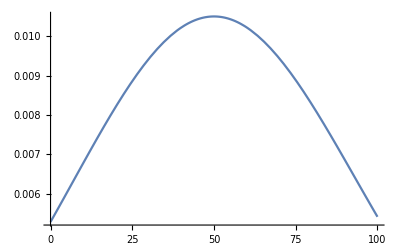

```mathematica
Plot[PDF[probDistVal,x],{x,0,100}]
```

```mathematica
RndList={};
For[i=1,i<1000,i++,
lbk=RandomVariate[GammaDistribution[zbk+1,1]];
probDist2=ProbabilityDistribution[(lsg+lbk)^zs*Exp[-lsg]/(Exp[lbk]* Gamma[1+zs,lbk]),{lsg,0,Infinity}];
r=N[RandomVariate[probDist2]];
AppendTo[RndList,r];
   ]
```

```mathematica
Print[RndList]
```

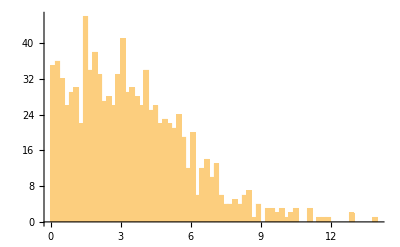

```mathematica
Histogram[RndList,50]
```

```mathematica
empDist=EmpiricalDistribution[RndList]
```

DataDistribution[…]

```mathematica
Median[empDist]
N[Median[probDistVal]]
StandardDeviation[empDist]
N[StandardDeviation[probDistVal]]
```

3.14831

3.71949

2.39714

2.403

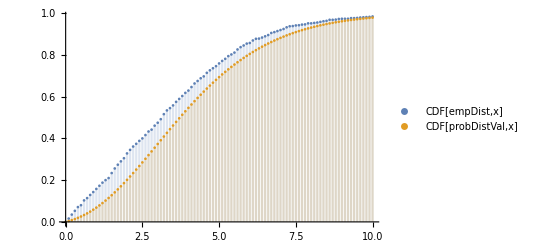

```mathematica
DiscretePlot[{CDF[empDist,x],CDF[probDistVal,x]},{x,0,10,0.1},PlotLegends->"Expressions"]
```

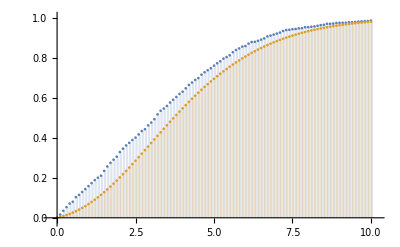

```mathematica
testDist=ProbabilityDistribution[lsg+lbk,{lsg,0,Infinity}]
```

ProbabilityDistribution[x+lbk,{x,0,∞}]

```mathematica
finalDist2=ParameterMixtureDistribution[probDist2,lbk\[Distributed]GammaDistribution[zbk+1,1]]
```

ParameterMixtureDistribution[ProbabilityDistribution[(ⅇ^(-x-lbk) (x+lbk)^5)/Gamma[6,lbk],{x,0,∞}],lbk\[Distributed]GammaDistribution[3,1]]

```mathematica
PDF[finalDist2,x]
```

PDF[ParameterMixtureDistribution[ProbabilityDistribution[(ⅇ^(-x-lbk) (x+lbk)^5)/Gamma[6,lbk],{x,0,∞}],lbk\[Distributed]GammaDistribution[3,1]],x]

```mathematica
Mean[finalDist2]
```

Gamma[3+zbk+zs]/Gamma[3+zbk]

```mathematica
Plot3D[Gamma[3+zbk+zs]/Gamma[3+zbk],{zbk,0,4},{zs,0,4},AxesLabel->{"zbk","zs"}]
```

-Graphics3D-

```mathematica
N[Median[finalDist2]]
```

1.25261×10^-8

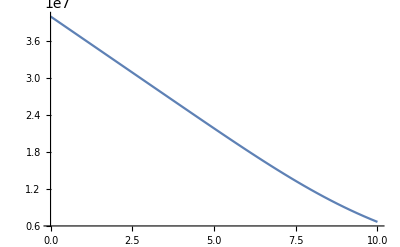

```mathematica
Plot[PDF[finalDist2,lsg],{lsg,0,10}]
```

```mathematica
Expand[(x+zbk)^zs]
```

65536+131072 x+114688 x^2+57344 x^3+17920 x^4+3584 x^5+448 x^6+32 x^7+x^8

```mathematica
Plot[PDF[GammaDistribution[zbk+1,1],x],{x,0,10}]
```

-Graphics-

```mathematica
normConst2=Integrate[PDF[finalDist2,lsg],{lsg,0,Infinity}]
```

6720

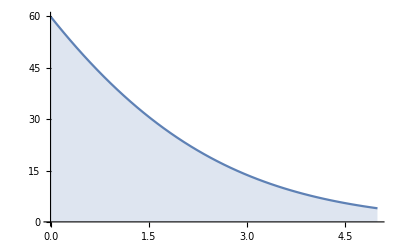

```mathematica
Plot[Evaluate[PDF[finalDist2,lsg]],{lsg,0,5},Filling->Axis]
```

```mathematica
𝒟=ParameterMixtureDistribution[NormalDistribution[a,1],a\[Distributed]UniformDistribution[{5,15}]]
```

ParameterMixtureDistribution[NormalDistribution[a,1],a\[Distributed]UniformDistribution[{5,15}]]

```mathematica
PDF[𝒟,x]
```

1/20 (-Erf[(5-x)/(√2)]+Erf[(15-x)/(√2)])

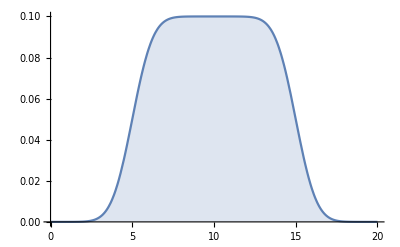

```mathematica
Plot[Evaluate[PDF[𝒟,x]],{x,0,20},Filling->Axis,PlotRange->All]
```

```mathematica
a=ProbabilityDistribution[NormalDistribution[10,1],{x,0,Infinity}]
```

ProbabilityDistribution[GammaDistribution[2,1.5],{x,0,∞}]

```mathematica
PDF[a,x]
```

PDF[a,x]

```mathematica
FindMaximum[Exp[-x]*(x+a)^b,x]
```

FindMaximum::nrnum: The function value -0.367879 (1.+a)^b is not a real number at {x} = {1.}.

FindMaximum[Exp[-x] (x+a)^b,x]